## Initial testing

#### Random stuff I wanted to hold on to

```mathematica
Udipole=(ℏ Γ^2)/(8δ)i/isat;
Udipole=(3π c^2)/(2 Subscript[ω, 0]^3)Γ/Δ intensity;
UdipoleCs[λ_,i_]:=3/(32 π^3 c^2)i((λCsD1^2 ΓCsD1)/(1-λCsD1/λ)+(λCsD2^2 ΓCsD2)/(1-λCsD2/λ));
UdipoleLi[λ_,i_]:=3/(32 π^3 c^2)i((λLiD1^2 ΓLiD1)/(1-λLiD1/λ)+(λLiD2^2 ΓLiD2)/(1-λLiD2/λ));

isatCsD2=1.6573 10; (* pi polarized, far off resonant *)
isatCsD1=1.6573 10; (* pi polarized, far off resonant *)
(* Lande g-Factors in Cs and Li *)
gFLi=gJ(F(F+1)-i(i+1)+J(J+1))/(2 F(F+1))/.{F->1/2,gJ->2.002,i->1,J->1/2};
gFCs=gJ(F(F+1)-i(i+1)+J(J+1))/(2 F(F+1))/.{F->3,gJ->2.002,i->7/2,J->1/2};
```

#### Physical constants

```mathematica
(* all in SI units *)
c=2.99792458 10^8;
μ0=4π 10^-7;
μB=9.2740095 10^-24;  (* Bohr magneton *)
ϵ0=8.854187 10^-12;
amu=1.66053906892 10^-27;
ℏ=1.054571628 10^-34;
kB=1.3806504 10^-23;
h=6.62607015 10^-34;
a0=0.52917720859 10^-10;
mCs=132.905451931 amu;
mLi=6.0151214 amu;
g=9.807;(* literally gravity g *)
λLiD1=670.992421 10^-9;
ΓLiD1=36.898 10^6; (* rad/s *)
λLiD2=670.977338 10^-9;
ΓLiD2=36.898 10^6;
λCsD1=894.59295986 10^-9;
ΓCsD1=28.743 10^6;
λCsD2=852.34727582 10^-9;
ΓCsD2=32.889 10^6;
gJCs=2.002;
gJLi=2.002;
λ1064=1064 10^-9;
(* all potentials will be in units of energy *)
Udipole=(π c^2 Γ)/(2 ω0^3)(2/Δ2+1/Δ1)Intensity; (* assumes pi linear polarization - see "OPTICAL DIPOLE TRAPS FOR NEUTRAL ATOMS" by Grimm, Weidemuller, and Ovchinnikov)*)
UdipoleCs1064=Udipole/.{Γ->ΓCsD2,ω0->2π c/λCsD2,Δ1->2π c(1/λ1064-1/λCsD1),Δ2->2π c(1/λ1064-1/λCsD2)};
UdipoleLi1064=Udipole/.{Γ->ΓLiD2,ω0->2π c/λLiD2,Δ1->2π c(1/λ1064-1/λLiD1),Δ2->2π c(1/λ1064-1/λLiD2)};
UgravityCs=mCs g z;
UgravityLi=mLi g z;
UBCs=μB gJCs -1/2 Bz/10000 ; (* Units here are Gauss for Magnetic field *)
UBLi=μB gJLi -1/2 Bz/10000 ;
(*TrapBottom[U_,m_]:=Module[{p},
p=FindMinimum[{U/m,x^2+y^2+z^2<10^-6},{{x,10^-6},{y,10^-6},{z,10^-6}}][[2]];
{p,{p[[1,2]],p[[2,2]],p[[3,2]]}}];
TrapFreqs[U_,m_]:=1/(2π){√D[U,{x,2}],√D[U,{y,2}],√D[U,{z,2}]}/(√m)/.TrapBottom[U,m][[1]];
TrapDepth[U_,m_]:=*)
```

#### Recreate final trap

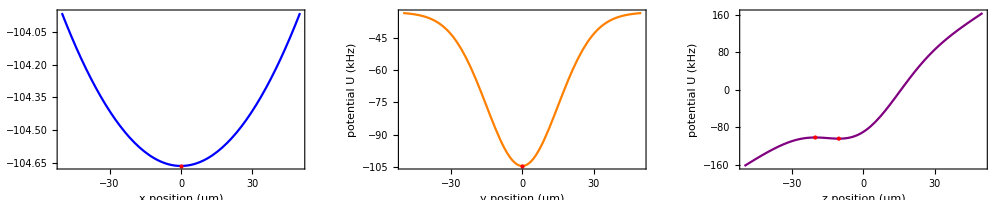

{6.52837,154.931,112.24}

2476.45

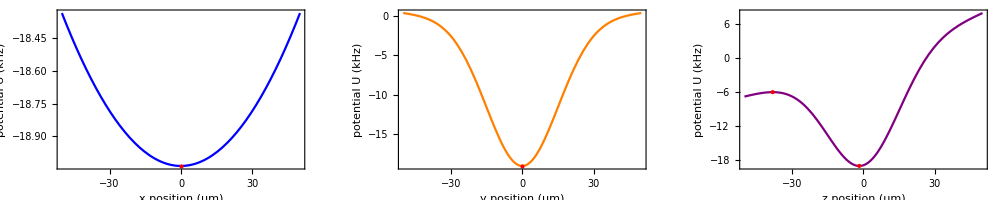

{30.687,375.725,373.148}

13059.

```mathematica
Bxycurvature=200000;
Bzcurvature=200000;
Bzgrad=0; (* Should be in units of Gauss/meter? *)
Final1064Power=26 10^-3;
Final1064Waist={30,30}10^-6;
PlotLims={50,50,50};
Final1064Intensity=Final1064Power/(π Final1064Waist[[1]]Final1064Waist[[2]]/2)Exp[-2 y^2/Final1064Waist[[1]]^2]Exp[-2 z^2/Final1064Waist[[2]]^2]; (* from RP Photonics https://www.rp-photonics.com/gaussian_beams.html *)
UtotCs=UBCs+UgravityCs+UdipoleCs1064/.{Intensity->Final1064Intensity,Bz->-Bxycurvature(x^2+y^2)-Bzcurvature z^2+Bzgrad z};
UtotLi=UBLi+UgravityLi+UdipoleLi1064/.{Intensity->Final1064Intensity,Bz->-Bxycurvature(x^2+y^2)-Bzcurvature z^2+Bzgrad z};

(* Cs first *)
Utot=UtotCs;
m =mCs;
{trapbottom,trapbottomcoords}=FindMinimum[{Utot/h,x^2+y^2+z^2<10^-6},{{x,0},{y,0},{z,0}}];
trapfreqs=1/(2π){√D[Utot,{x,2}],√D[Utot,{y,2}],√D[Utot,{z,2}]}/(√m)/.trapbottomcoords;
{trapdepth,trapedge}=FindMaximum[{Utot/h-trapbottom/.{x->0,y->0},z<trapbottomcoords[[3,2]],z>-10^-3},{z,trapbottomcoords[[3,2]]}];
(* plot time *)
GraphicsRow[{Plot[Utot/(1000h)/.{x->r/10^6,trapbottomcoords[[2]],trapbottomcoords[[3]]},{r,-PlotLims[[1]],PlotLims[[1]]},PlotStyle->Blue,ImageSize->Medium,Frame->True,FrameLabel->{"x position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[1,2]] 10^6,trapbottom/1000}]}],
Plot[Utot/(1000h)/.{trapbottomcoords[[1]],y->r/10^6,trapbottomcoords[[3]]},{r,-PlotLims[[2]],PlotLims[[2]]},PlotStyle->Orange,ImageSize->Medium,Frame->True,FrameLabel->{"y position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[2,2]] 10^6,trapbottom/1000}]}],
Show[Plot[Utot/(1000h)/.{trapbottomcoords[[1]],trapbottomcoords[[2]],z->r/10^6},{r,-PlotLims[[3]],PlotLims[[3]]},PlotStyle->Purple,ImageSize->Medium,Frame->True,FrameLabel->{"z position (µm)", "potential U (kHz)"}],ListPlot[{{trapbottomcoords[[3,2]] 10^6,trapbottom/1000},{trapedge[[1,2]] 10^6,(trapbottom+trapdepth)/1000}},PlotStyle->{PointSize[Large],Red}]]},ImageSize->{1000,200}]
trapfreqs
trapdepth

(* Li time *)
Utot=UtotLi;
m =mLi;
{trapbottom,trapbottomcoords}=FindMinimum[{Utot/h,x^2+y^2+z^2<10^-6},{{x,0},{y,0},{z,0}}];
trapfreqs=1/(2π){√D[Utot,{x,2}],√D[Utot,{y,2}],√D[Utot,{z,2}]}/(√m)/.trapbottomcoords;
{trapdepth,trapedge}=FindMaximum[{Utot/h-trapbottom/.{x->0,y->0},z<trapbottomcoords[[3,2]],z>-10^-3},{z,trapbottomcoords[[3,2]]}];
(* plot time *)
GraphicsRow[{Plot[Utot/(1000h)/.{x->r/10^6,trapbottomcoords[[2]],trapbottomcoords[[3]]},{r,-PlotLims[[1]],PlotLims[[1]]},PlotStyle->Blue,ImageSize->Medium,Frame->True,FrameLabel->{"x position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[1,2]] 10^6,trapbottom/1000}]}],
Plot[Utot/(1000h)/.{trapbottomcoords[[1]],y->r/10^6,trapbottomcoords[[3]]},{r,-PlotLims[[2]],PlotLims[[2]]},PlotStyle->Orange,ImageSize->Medium,Frame->True,FrameLabel->{"y position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[2,2]] 10^6,trapbottom/1000}]}],
Show[Plot[Utot/(1000h)/.{trapbottomcoords[[1]],trapbottomcoords[[2]],z->r/10^6},{r,-PlotLims[[3]],PlotLims[[3]]},PlotStyle->Purple,ImageSize->Medium,Frame->True,FrameLabel->{"z position (µm)", "potential U (kHz)"}],ListPlot[{{trapbottomcoords[[3,2]] 10^6,trapbottom/1000},{trapedge[[1,2]] 10^6,(trapbottom+trapdepth)/1000}},PlotStyle->{PointSize[Large],Red}]]},ImageSize->{1000,200}]
trapfreqs
trapdepth
```

#### OTOP attempt

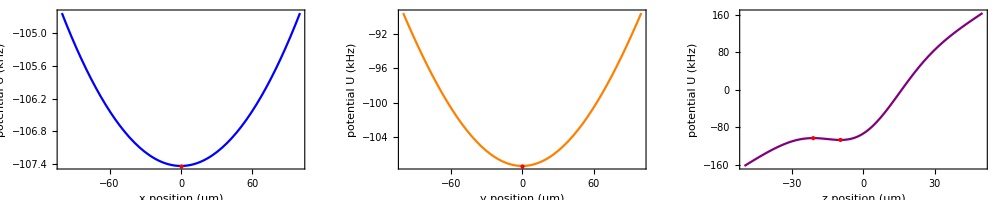

{6.52837,17.2936,122.591}

3910.34

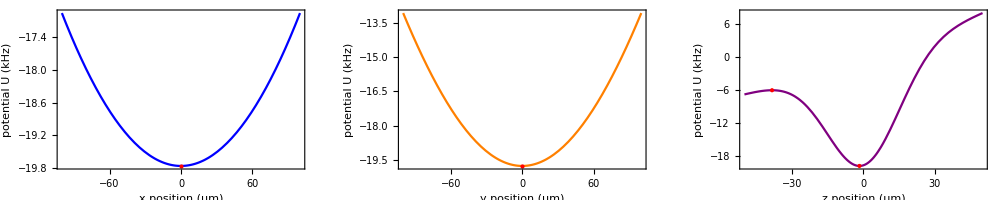

{30.687,48.9759,380.497}

13753.3

```mathematica
Bxycurvature=200000;
Bzcurvature=200000;
Bzgrad=0; (* Should be in units of Gauss/meter? *)
Final1064Power=270 10^-3;
Final1064Waist={300,30}10^-6;
PlotLims={100,100,50};
Final1064Intensity=Final1064Power/(π Final1064Waist[[1]]Final1064Waist[[2]]/2)Exp[-2 y^2/Final1064Waist[[1]]^2]Exp[-2 z^2/Final1064Waist[[2]]^2]; (* from RP Photonics https://www.rp-photonics.com/gaussian_beams.html *)
UtotCs=UBCs+UgravityCs+UdipoleCs1064/.{Intensity->Final1064Intensity,Bz->-Bxycurvature(x^2+y^2)-Bzcurvature z^2+Bzgrad z};
UtotLi=UBLi+UgravityLi+UdipoleLi1064/.{Intensity->Final1064Intensity,Bz->-Bxycurvature(x^2+y^2)-Bzcurvature z^2+Bzgrad z};

(* Cs first *)
Utot=UtotCs;
m =mCs;
{trapbottom,trapbottomcoords}=FindMinimum[{Utot/h,x^2+y^2+z^2<10^-6},{{x,0},{y,0},{z,0}}];
trapfreqs=1/(2π){√D[Utot,{x,2}],√D[Utot,{y,2}],√D[Utot,{z,2}]}/(√m)/.trapbottomcoords;
{trapdepth,trapedge}=FindMaximum[{Utot/h-trapbottom/.{x->0,y->0},z<trapbottomcoords[[3,2]],z>-10^-3},{z,trapbottomcoords[[3,2]]}];
(* plot time *)
GraphicsRow[{Plot[Utot/(1000h)/.{x->r/10^6,trapbottomcoords[[2]],trapbottomcoords[[3]]},{r,-PlotLims[[1]],PlotLims[[1]]},PlotStyle->Blue,ImageSize->Medium,Frame->True,FrameLabel->{"x position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[1,2]] 10^6,trapbottom/1000}]}],
Plot[Utot/(1000h)/.{trapbottomcoords[[1]],y->r/10^6,trapbottomcoords[[3]]},{r,-PlotLims[[2]],PlotLims[[2]]},PlotStyle->Orange,ImageSize->Medium,Frame->True,FrameLabel->{"y position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[2,2]] 10^6,trapbottom/1000}]}],
Show[Plot[Utot/(1000h)/.{trapbottomcoords[[1]],trapbottomcoords[[2]],z->r/10^6},{r,-PlotLims[[3]],PlotLims[[3]]},PlotStyle->Purple,ImageSize->Medium,Frame->True,FrameLabel->{"z position (µm)", "potential U (kHz)"}],ListPlot[{{trapbottomcoords[[3,2]] 10^6,trapbottom/1000},{trapedge[[1,2]] 10^6,(trapbottom+trapdepth)/1000}},PlotStyle->{PointSize[Large],Red}]]},ImageSize->{1000,200}]
trapfreqs
trapdepth

(* Li time *)
Utot=UtotLi;
m =mLi;
{trapbottom,trapbottomcoords}=FindMinimum[{Utot/h,x^2+y^2+z^2<10^-6},{{x,0},{y,0},{z,0}}];
trapfreqs=1/(2π){√D[Utot,{x,2}],√D[Utot,{y,2}],√D[Utot,{z,2}]}/(√m)/.trapbottomcoords;
{trapdepth,trapedge}=FindMaximum[{Utot/h-trapbottom/.{x->0,y->0},z<trapbottomcoords[[3,2]],z>-10^-2},{z,trapbottomcoords[[3,2]]}];
(* plot time *)
GraphicsRow[{Plot[Utot/(1000h)/.{x->r/10^6,trapbottomcoords[[2]],trapbottomcoords[[3]]},{r,-PlotLims[[1]],PlotLims[[1]]},PlotStyle->Blue,ImageSize->Medium,Frame->True,FrameLabel->{"x position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[1,2]] 10^6,trapbottom/1000}]}],
Plot[Utot/(1000h)/.{trapbottomcoords[[1]],y->r/10^6,trapbottomcoords[[3]]},{r,-PlotLims[[2]],PlotLims[[2]]},PlotStyle->Orange,ImageSize->Medium,Frame->True,FrameLabel->{"y position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[2,2]] 10^6,trapbottom/1000}]}],
Show[Plot[Utot/(1000h)/.{trapbottomcoords[[1]],trapbottomcoords[[2]],z->r/10^6},{r,-PlotLims[[3]],PlotLims[[3]]},PlotStyle->Purple,ImageSize->Medium,Frame->True,FrameLabel->{"z position (µm)", "potential U (kHz)"}],ListPlot[{{trapbottomcoords[[3,2]] 10^6,trapbottom/1000},{trapedge[[1,2]] 10^6,(trapbottom+trapdepth)/1000}},PlotStyle->{PointSize[Large],Red}]]},ImageSize->{1000,200}]
trapfreqs
trapdepth
```

#### V Lat attempt

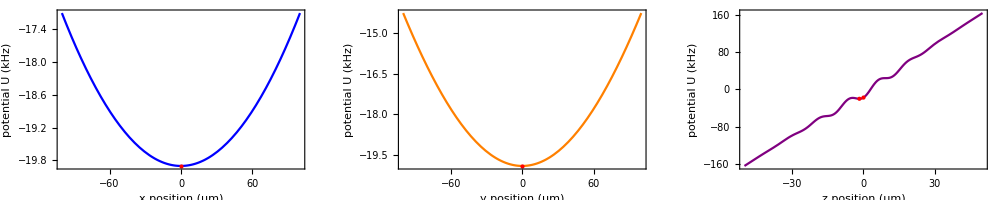

{6.52837,9.53799,326.111}

2606.83

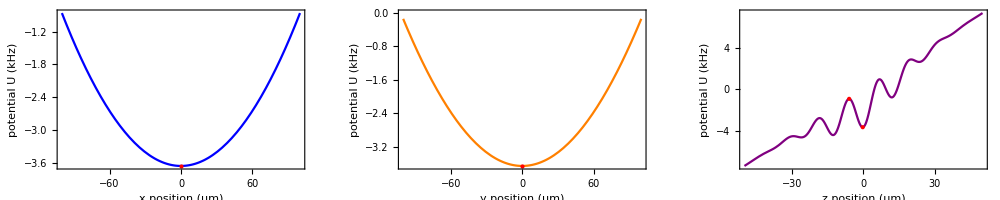

{30.687,34.8055,869.702}

2742.99

```mathematica
Bxycurvature=200000;
Bzcurvature=0;
Bzgrad=0; (* Should be in units of Gauss/meter? *)
Final1064Power=50 10^-3;
Final1064Waist={300,30}10^-6;
Final1064Angle=1/24;
PlotLims={100,100,50};
Final1064Intensity=Final1064Power/(π Final1064Waist[[1]]Final1064Waist[[2]]/2)Exp[-2 y^2/Final1064Waist[[1]]^2]Exp[-2 z^2/Final1064Waist[[2]]^2] Cos[(2π Final1064Angle)/λ1064 z]^2; (* from RP Photonics https://www.rp-photonics.com/gaussian_beams.html *)
UtotCs=UBCs+UgravityCs+UdipoleCs1064/.{Intensity->Final1064Intensity,Bz->-Bxycurvature(x^2+y^2)-Bzcurvature z^2+Bzgrad z};
UtotLi=UBLi+UgravityLi+UdipoleLi1064/.{Intensity->Final1064Intensity,Bz->-Bxycurvature(x^2+y^2)-Bzcurvature z^2+Bzgrad z};

(* Cs first *)
Utot=UtotCs;
m =mCs;
{trapbottom,trapbottomcoords}=FindMinimum[{Utot/h,x^2+y^2+z^2<10^-6},{{x,0},{y,0},{z,0}}];
trapfreqs=1/(2π){√D[Utot,{x,2}],√D[Utot,{y,2}],√D[Utot,{z,2}]}/(√m)/.trapbottomcoords;
{trapdepth,trapedge}=FindMaximum[{Utot/h-trapbottom/.{x->0,y->0},z<0,z>-10^-3},{z,trapbottomcoords[[3,2]]}];
(* plot time *)
GraphicsRow[{Plot[Utot/(1000h)/.{x->r/10^6,trapbottomcoords[[2]],trapbottomcoords[[3]]},{r,-PlotLims[[1]],PlotLims[[1]]},PlotStyle->Blue,ImageSize->Medium,Frame->True,FrameLabel->{"x position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[1,2]] 10^6,trapbottom/1000}]}],
Plot[Utot/(1000h)/.{trapbottomcoords[[1]],y->r/10^6,trapbottomcoords[[3]]},{r,-PlotLims[[2]],PlotLims[[2]]},PlotStyle->Orange,ImageSize->Medium,Frame->True,FrameLabel->{"y position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[2,2]] 10^6,trapbottom/1000}]}],
Show[Plot[Utot/(1000h)/.{trapbottomcoords[[1]],trapbottomcoords[[2]],z->r/10^6},{r,-PlotLims[[3]],PlotLims[[3]]},PlotStyle->Purple,ImageSize->Medium,Frame->True,FrameLabel->{"z position (µm)", "potential U (kHz)"}],ListPlot[{{trapbottomcoords[[3,2]] 10^6,trapbottom/1000},{trapedge[[1,2]] 10^6,(trapbottom+trapdepth)/1000}},PlotStyle->{PointSize[Large],Red}]]},ImageSize->{1000,200}]
trapfreqs
trapdepth

(* Li time *)
Utot=UtotLi;
m =mLi;
{trapbottom,trapbottomcoords}=FindMinimum[{Utot/h,x^2+y^2+z^2<10^-6},{{x,0},{y,0},{z,0}}];
trapfreqs=1/(2π){√D[Utot,{x,2}],√D[Utot,{y,2}],√D[Utot,{z,2}]}/(√m)/.trapbottomcoords;
{trapdepth,trapedge}=FindMaximum[{Utot/h-trapbottom/.{x->0,y->0},z<trapbottomcoords[[3,2]],z>-10^-2},{z,trapbottomcoords[[3,2]]}];
(* plot time *)
GraphicsRow[{Plot[Utot/(1000h)/.{x->r/10^6,trapbottomcoords[[2]],trapbottomcoords[[3]]},{r,-PlotLims[[1]],PlotLims[[1]]},PlotStyle->Blue,ImageSize->Medium,Frame->True,FrameLabel->{"x position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[1,2]] 10^6,trapbottom/1000}]}],
Plot[Utot/(1000h)/.{trapbottomcoords[[1]],y->r/10^6,trapbottomcoords[[3]]},{r,-PlotLims[[2]],PlotLims[[2]]},PlotStyle->Orange,ImageSize->Medium,Frame->True,FrameLabel->{"y position (µm)", "potential U (kHz)"},Epilog->{Red,PointSize@Large,Point[{trapbottomcoords[[2,2]] 10^6,trapbottom/1000}]}],
Show[Plot[Utot/(1000h)/.{trapbottomcoords[[1]],trapbottomcoords[[2]],z->r/10^6},{r,-PlotLims[[3]],PlotLims[[3]]},PlotStyle->Purple,ImageSize->Medium,Frame->True,FrameLabel->{"z position (µm)", "potential U (kHz)"}],ListPlot[{{trapbottomcoords[[3,2]] 10^6,trapbottom/1000},{trapedge[[1,2]] 10^6,(trapbottom+trapdepth)/1000}},PlotStyle->{PointSize[Large],Red}]]},ImageSize->{1000,200}]
trapfreqs
trapdepth
```

### V Lattice math

```mathematica
E1=Exp[I k(x Cos[θ]+y Sin[θ])];
E2=Exp[I k(x Cos[θ]-y Sin[θ])];
FullSimplify[(E1+E2)Conjugate[E1+E2],Assumptions->{x>0,y>0,k>0,θ>0}]
```

4 Cos[k y Sin[θ]]^2

## Developing a pipeline to calculate all properties of mixture given an initial configuration

### Constants

```mathematica
(* all in SI units *)
c=2.99792458 10^8;
μ0=4π 10^-7;
μB=9.2740095 10^-24;  (* Bohr magneton *)
ϵ0=8.854187 10^-12;
amu=1.66053906892 10^-27;
ℏ=1.054571628 10^-34;
kB=1.3806504 10^-23;
h=6.62607015 10^-34;
a0=0.52917720859 10^-10;
mCs=132.905451931 amu;
mLi=6.0151214 amu;
g=9.807;(* literally gravity g *)
λLiD1=670.992421 10^-9;
ΓLiD1=36.898 10^6; (* rad/s *)
λLiD2=670.977338 10^-9;
ΓLiD2=36.898 10^6;
λCsD1=894.59295986 10^-9;
ΓCsD1=28.743 10^6;
λCsD2=852.34727582 10^-9;
ΓCsD2=32.889 10^6;
gJCs=2.002;
gJLi=2.002;
λ1064=1064 10^-9;
(* all potentials will be in units of energy *)
Udipole=(π c^2 Γ)/(2 ω0^3)(2/Δ2+1/Δ1)Intensity; (* assumes pi linear polarization - see "OPTICAL DIPOLE TRAPS FOR NEUTRAL ATOMS" by Grimm, Weidemuller, and Ovchinnikov)*)
UdipoleCs1064=Udipole/.{Γ->ΓCsD2,ω0->2π c/λCsD2,Δ1->2π c(1/λ1064-1/λCsD1),Δ2->2π c(1/λ1064-1/λCsD2)};
UdipoleLi1064=Udipole/.{Γ->ΓLiD2,ω0->2π c/λLiD2,Δ1->2π c(1/λ1064-1/λLiD1),Δ2->2π c(1/λ1064-1/λLiD2)};
UgravityCs=mCs g z;
UgravityLi=mLi g z;
UBCs=μB gJCs -1/2 Bz/10000 ; (* Units here are Gauss for Magnetic field *)
UBLi=μB gJLi -1/2 Bz/10000 ;
```

### Testing

Cs trap frequencies are {6.52837, 154.805, 111.611} Hz

Cs trap depth is 2392.23 Hz = 114.809 nK

Cs chemical potential is 632.338 Hz = 30.3474 nK

Cs Thomas-Fermi radii are {47.5047, 2.00335, 2.77865} µm

Li trap frequencies are {30.687, 375.708, 371.831} Hz

Li trap depth is 12664.4 Hz = 607.795 nK

Li Fermi energy is 6359.66 Hz = 305.215 nK

Li Thomas-Fermi radii are {150.653, 12.305, 12.4333} µm

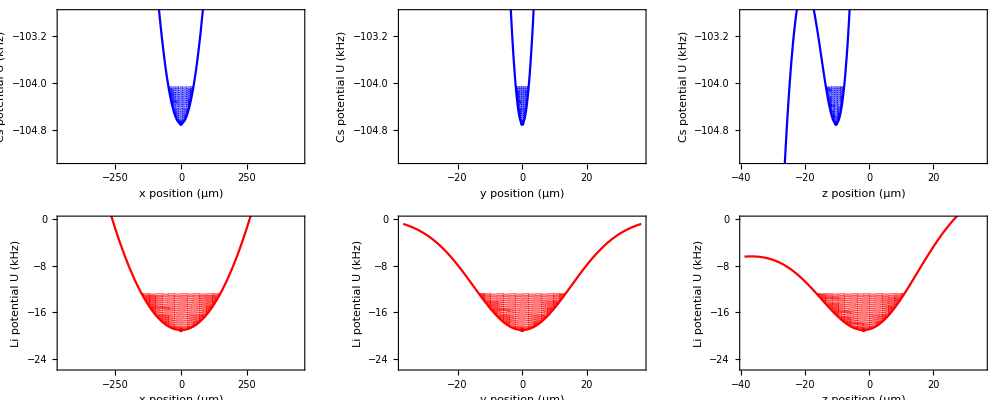

```mathematica
Bxycurvature=200000; (* Picked to match magnetic trap frequency *)
Bzcurvature=0; (* Should figure this relationship out but it doesn't matter that much *)
Bzgrad=0; (* Should be in units of Gauss/meter? *)
Bzfield=-Bxycurvature(x^2+y^2)-Bzcurvature z^2+Bzgrad z;
FinalTrapPower=26 10^-3;
FinalTrapWaist={30,30}10^-6;
FinalTrapAngle=1/24;
FinalTrapIntensity=FinalTrapPower/(π FinalTrapWaist[[1]]FinalTrapWaist[[2]]/2)Exp[-2 y^2/FinalTrapWaist[[1]]^2]Exp[-2 z^2/FinalTrapWaist[[2]]^2];
PlotLims={100,100,50};
aBB=277;
NCs=20000;
NLi=10000;

(* Inputs to this next stage should basically just be Bzfield, FinalTrapIntensity, PlotLims, NCs, NLi, aCs *)
UtotCs=UBCs+UgravityCs+UdipoleCs1064/.{Intensity->FinalTrapIntensity,Bz->Bzfield};
UtotLi=UBLi+UgravityLi+UdipoleLi1064/.{Intensity->FinalTrapIntensity,Bz->Bzfield};

(* Cs first *)
{cstrapbottom,cstrapbottomcoords}=FindMinimum[{UtotCs/h,x^2+y^2+z^2<10^-6},{{x,0},{y,0},{z,0}}];
cstrapfreqs=1/(2π){√D[UtotCs,{x,2}],√D[UtotCs,{y,2}],√D[UtotCs,{z,2}]}/(√mCs)/.cstrapbottomcoords;
{cstrapdepth,cstrapedge}=FindMaximum[{UtotCs/h-cstrapbottom/.{x->0,y->0},z<0,z>-10^-3},{z,cstrapbottomcoords[[3,2]]}];
(* here's where the BEC stuff starts *)
cstrapωs=2π cstrapfreqs;
csωho=(cstrapωs[[1]] cstrapωs[[2]] cstrapωs[[3]])^(1/3);
csaho=√(ℏ/(mCs csωho));
μ=(ℏ csωho)/2((15 NCs aBB a0)/csaho)^(2/5);
csrTFs=√((2μ)/(mCs cstrapωs^2));
StringTemplate["Cs trap frequencies are `` Hz"][cstrapfreqs]
StringTemplate["Cs trap depth is `` Hz = `` nK"][cstrapdepth, cstrapdepth*h*10^9/kB]
StringTemplate["Cs chemical potential is `` Hz = `` nK"][μ/h,μ*10^9/kB]
StringTemplate["Cs Thomas-Fermi radii are `` µm"][10^6 csrTFs]

(* Li second *)
{litrapbottom,litrapbottomcoords}=FindMinimum[{UtotLi/h,x^2+y^2+z^2<10^-6},{{x,0},{y,0},{z,0}}];
litrapfreqs=1/(2π){√D[UtotLi,{x,2}],√D[UtotLi,{y,2}],√D[UtotLi,{z,2}]}/(√mLi)/.litrapbottomcoords;
{litrapdepth,litrapedge}=FindMaximum[{UtotLi/h-litrapbottom/.{x->0,y->0},z<0,z>-10^-3},{z,litrapbottomcoords[[3,2]]}];
(* here's where the Fermi gas stuff starts *)
litrapωs=2π litrapfreqs;
liωho=(litrapωs[[1]] litrapωs[[2]] litrapωs[[3]])^(1/3);
EF=(6*NLi)^(1/3)ℏ liωho;
lirTFs=√((2EF)/(mLi litrapωs^2));
StringTemplate["Li trap frequencies are `` Hz"][litrapfreqs]
StringTemplate["Li trap depth is `` Hz = `` nK"][litrapdepth, litrapdepth*h*10^9/kB]
StringTemplate["Li Fermi energy is `` Hz = `` nK"][EF/h,EF*10^9/kB]
StringTemplate["Li Thomas-Fermi radii are `` µm"][10^6 lirTFs]


(* plot time *)
csblue=Blue;
lired=Red;
csxlims=Table[10^6{cstrapbottomcoords[[ii,2]]-3 csrTFs[[ii]],cstrapbottomcoords[[ii,2]]+3 csrTFs[[ii]]},{ii,1,3}];
lixlims=Table[10^6{litrapbottomcoords[[ii,2]]-3 lirTFs[[ii]],litrapbottomcoords[[ii,2]]+3 lirTFs[[ii]]},{ii,1,3}];
xlims=Table[{Min[csxlims[[ii,1]],lixlims[[ii,1]]],Max[csxlims[[ii,2]],lixlims[[ii,2]]]},{ii,1,3}];
xvarstrs={"x","y","z"};
xvars={x,y,z};
GraphicsGrid[
{Table[
Show[Plot[UtotCs/(1000h)/.Join[{xvars[[ii]]->r/10^6},cstrapbottomcoords],{r,xlims[[ii,1]],xlims[[ii,2]]},Frame->True,FrameLabel->{StringTemplate["`` position (µm)"][xvarstrs[[ii]]], "Cs potential U (kHz)"},PlotStyle->csblue],
RegionPlot[(UtotCs/(1000h)/.Join[{xvars[[ii]]->r/10^6},cstrapbottomcoords])<w&&w<(cstrapbottom+μ/h)/1000,{r,csxlims[[ii,1]],csxlims[[ii,2]]},{w,cstrapbottom/1000,(cstrapbottom+μ/h)/1000},BoundaryStyle->None,PlotStyle->{csblue,Opacity[0.3]}],
ListPlot[{{cstrapbottomcoords[[ii,2]] 10^6,cstrapbottom/1000}},PlotStyle->{PointSize[Large],csblue}],PlotRange->{{xlims[[ii,1]],xlims[[ii,2]]},{(cstrapbottom-μ/h)/1000,(cstrapbottom+3 μ/h)/1000}}],{ii,1,3}],
Table[
Show[Plot[UtotLi/(1000h)/.Join[{xvars[[ii]]->r/10^6},litrapbottomcoords],{r,xlims[[ii,1]],xlims[[ii,2]]},Frame->True,FrameLabel->{StringTemplate["`` position (µm)"][xvarstrs[[ii]]], "Li potential U (kHz)"},PlotStyle->lired],
RegionPlot[(UtotLi/(1000h)/.Join[{xvars[[ii]]->r/10^6},litrapbottomcoords])<w&&w<(litrapbottom+EF/h)/1000,{r,lixlims[[ii,1]],lixlims[[ii,2]]},{w,litrapbottom/1000,(litrapbottom+EF/h)/1000},BoundaryStyle->None,PlotStyle->{lired,Opacity[0.3]}],
ListPlot[{{litrapbottomcoords[[ii,2]] 10^6,litrapbottom/1000}},PlotStyle->{PointSize[Large],lired}],PlotRange->{{xlims[[ii,1]],xlims[[ii,2]]},{(litrapbottom-EF/h)/1000,(litrapbottom+3 EF/h)/1000}}],{ii,1,3}]}
,ImageSize->{1000,400}]
```